# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["G:\\My Drive\\Doctorado\\OCTAVO SEMESTRE\\Prethermalization\\prethermalization 50 states\\Old skeleton data and figures\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14];
```

```mathematica
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

# S(t) results

## parameters used

```mathematica
L=8;
J=1;
tlist=Table[10^i,{i,-1,10,0.0010}];
tlist//Length
```

11001

```mathematica
glist=Table[10^i,{i,-10,-1,0.2}];
glist=Sort[AppendTo[glist,0.0]];
glist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

47

## Log-Log scale

```mathematica
L=8;
J=1;
q=0.3;
```

```mathematica
data=Import["G:\\My Drive\\Doctorado\\OCTAVO SEMESTRE\\Prethermalization\\prethermalization 50 states\\NEW SKELETON FIGURES\\LRN_L_8_h_0.1_g_"<>ToString[q]<>"_.m"];
```

```mathematica
limitzero=Mean[Mean[data[[1]]][[-1000;;-1]]];
limitone=Mean[data[[-1]]][[-200;;-1]][[-1]];
pageVal=N[pageEntropy[L/2,L/2]];
```

```mathematica
plots=Table[ListLogLogPlot[{Transpose[{tlist,Mean[data[[i]]]}],MovingAverage[Transpose[{tlist,Mean[data[[i]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.01]],Directive[reds[[i]],Opacity[1]]},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[q],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},GridLines->None,PlotRange->{All,{1.7,pageVal}}],{i,Length[glist]}];
```

```mathematica
Show[plots]
```

-Graphics-

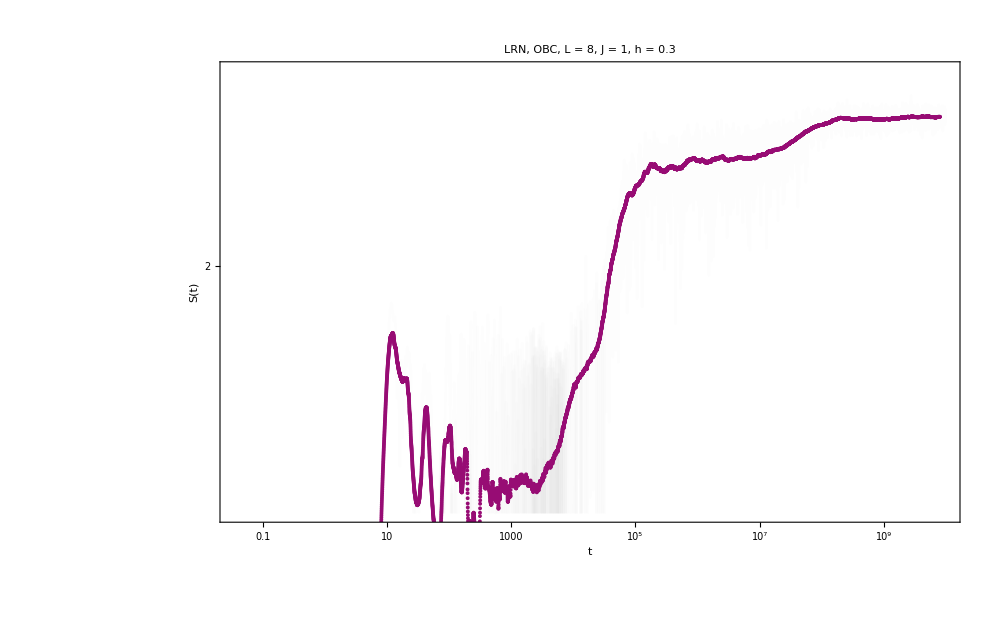

```mathematica
plots[[30]]
```

# power laws

## LRN

```mathematica
Clear[threshold];
threshold[value_,data_List]:=Module[{pos},
(*Find index of first point with S>=threshold*)
pos=FirstPosition[data[[All,2]],_?(#>=value&),Missing["NoCrossing"]];
If[pos===Missing["NoCrossing"],Missing["NoCrossing"],
data[[First[pos],1]]]
];
```

```mathematica
series = Table[MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200], {h,Length[hlist]}];
```

```mathematica
pairs=Table[{hlist[[i]],threshold[2.,series[[i]]]},{i,Length[series]}];
Table[{i,hlist[[i]],threshold[0.7,series[[i]]]},{i,Length[series]}]//TableForm
```

1 | 2.51189×10^-6 | 0.824766
2 | 3.98107×10^-6 | 0.824766
3 | 6.30957×10^-6 | 0.824766
4 | 0.00001 | 0.824766
5 | 0.0000158489 | 0.824766
6 | 0.0000251189 | 0.824766
7 | 0.0000398107 | 0.824766
8 | 0.0000630957 | 0.824766
9 | 0.0001 | 0.824766
10 | 0.000158489 | 0.824766
11 | 0.000251189 | 0.824766
12 | 0.000398107 | 0.824766
13 | 0.000630957 | 0.824766
14 | 0.001 | 0.824766
15 | 0.00158489 | 0.824766
16 | 0.00251189 | 0.824766
17 | 0.00398107 | 0.824766
18 | 0.00630957 | 0.824766
19 | 0.01 | 0.824766
20 | 0.0158489 | 0.824766
21 | 0.0251189 | 0.824766
22 | 0.0398107 | 0.824766
23 | 0.0630957 | 0.824766
24 | 0.1 | 0.824766

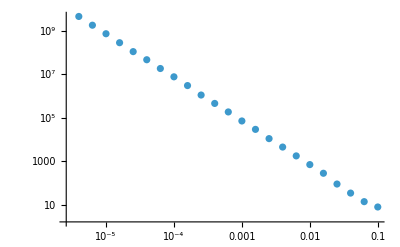

```mathematica
ListLogLogPlot[pairs,PlotRange->All]
```

```mathematica
newpairs=pairs[[3;;-1]];
```

```mathematica
pairs[[3;;-1]]//TableForm
```

6.30957×10^-6 | 1.7961×10^9
0.00001 | 7.28334×10^8
0.0000158489 | 2.82053×10^8
0.0000251189 | 1.09731×10^8
0.0000398107 | 4.64869×10^7
0.0000630957 | 1.83794×10^7
0.0001 | 7.6266×10^6
0.000158489 | 3.02225×10^6
0.000251189 | 1.11002×10^6
0.000398107 | 456384.
0.000630957 | 185494.
0.001 | 71339.6
0.00158489 | 29331.3
0.00251189 | 11023.8
0.00398107 | 4511.6
0.00630957 | 1771.46
0.01 | 705.23
0.0158489 | 282.053
0.0251189 | 90.2258
0.0398107 | 34.6203
0.0630957 | 13.9743
0.1 | 7.94933

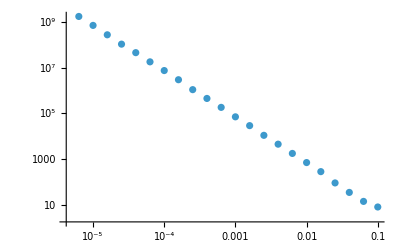

```mathematica
ListLogLogPlot[newpairs,PlotRange->All]
```

```mathematica
Sstar=2.0;
```

```mathematica
(*power-law fit:log T=log a+b log g*)
logData=Transpose[{Log[newpairs[[All,1]]],Log[newpairs[[All,2]]]}];
lm=LinearModelFit[logData,{1,z},z];
{logA,b}=lm["BestFitParameters"];
a=Exp[logA];
model[g_]:=a g^b;
```

```mathematica
{xmin,xmax}=MinMax[newpairs[[All,1]]];
fitCurve=Table[{g,model[g]},{g,xmin,xmax,(xmax-xmin)/300.}];
lineKey=Graphics[{Red,Dashed,Thick,Line[{{0,1.3},{1,1.3}}]},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[0],ImagePadding->6,ImageSize->50,AspectRatio->1/6,Background->White];
powLbl=Framed[Row[{lineKey,Style["\!\(\*SubscriptBox[\(T\), \(M\)]\) ∝"TraditionalForm@Superscript["g",NumberForm[b,{4,3}]],30,Black]}],Background->White,FrameStyle->GrayLevel[.6],RoundingRadius->6,FrameMargins->3];
```

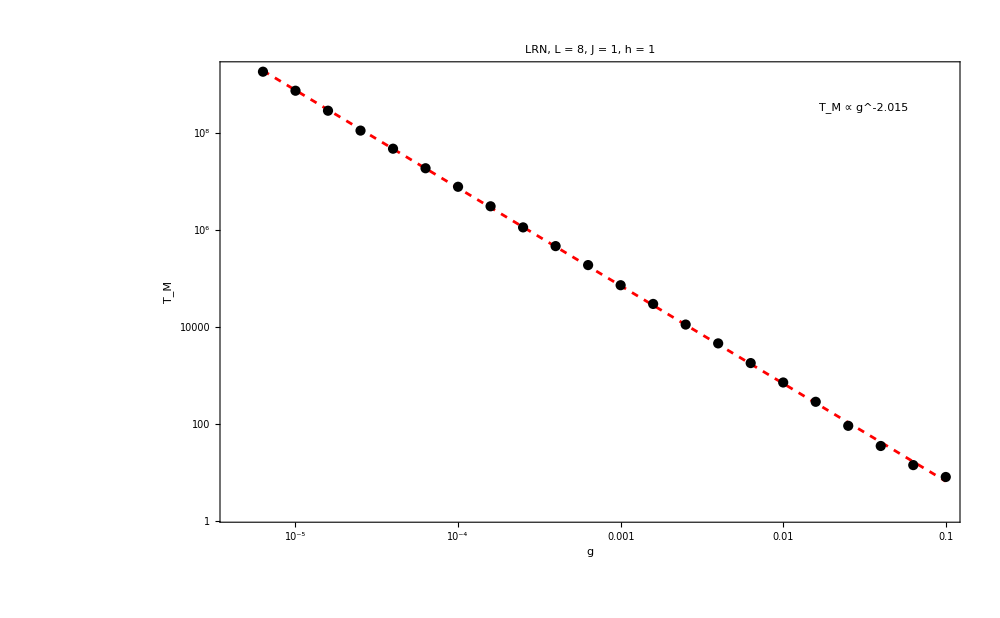

```mathematica
powerplot=ListLogLogPlot[{newpairs,fitCurve},Joined->{False,True},PlotStyle->{Black,{Red,Dashed}},ImageSize->1000,PlotTheme->"Detailed",FrameStyle->Directive[Black,30],PlotLabel->Style["LRN, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[q],40,Black],FrameLabel->{Style["g",35,Black],Rotate[Style["\!\(\*SubscriptBox[\(T\), \(M\)]\)",35,Black],-90 Degree]},GridLines->None,PlotRange->All,Epilog->Inset[powLbl,Scaled[{0.87,0.90}]]]
```

```mathematica
Export["L_"<>ToString[L]<>"_LRN_powerplot_entropy_h_"<>ToString[q]<>"_.png",powerplot]
```

L_8_LRN_powerplot_entropy_h_1_.png

# Derivative,LRN, h =1

```mathematica
data=Import["G:\\My Drive\\Doctorado\\OCTAVO SEMESTRE\\Prethermalization\\prethermalization 50 states\\NEW SKELETON FIGURES\\LRN_L_8_h_0.1_g_1._.m"];
```

```mathematica
(*Since tlist is logarithmically spaced (1000 pts/decade),*)
(*we compute dS/d(log t)=t*dS/dt via finite differences*)
(*on the log-spaced grid.This naturally weights all decades*)
(*equally and reveals the plateau as dS/d(log t)≈0.*)(* ================================================================*)(*---Core derivative function---*)(*Input:{tlist,entropy} both length-N vectors.*)(*maW=moving average window applied BEFORE differentiating.*)(*Output:{tlist (trimmed),dS/d(log10 t)} same length.*)logTimeDerivative[tgrid_,entropy_,maW_:200]:=Module[{n=Length[tgrid],logt,sSmooth,dsdt,tmid},
logt=Log10[tgrid];
(*Smooth first,then differentiate*)
sSmooth=If[maW>1,Table[Mean[entropy[[Max[1,i-Floor[(maW-1)/2]];;Min[n,i+Floor[(maW-1)/2]]]]],{i,n}],entropy];
(*Central finite difference on log10(t) grid*)
dsdt=Table[(sSmooth[[i+1]]-sSmooth[[i-1]])/(logt[[i+1]]-logt[[i-1]]),{i,2,n-1}];
tmid=tgrid[[2;;-2]];
{tmid,dsdt}]
```

```mathematica
logDerivAnalysis[data_,paramList_,tgrid_,regime_String,LL_Integer,maW_:200]:=Module[{nParams,meanS,tmid,dSdlogt,logMin,logMax,colors,curves,plt,cf},
nParams=Length[paramList];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
logMin=Log10[Min[Select[paramList,#>0&]]];
logMax=Log10[Max[paramList]];
colors=Table[If[paramList[[h]]==0,Gray,cf[Rescale[Log10[paramList[[h]]],{logMin,logMax},{0,1}]]],{h,nParams}];
(*Compute derivative for each parameter value*)
curves=Table[meanS=If[MatrixQ[data[[h]]],Mean[data[[h]]],data[[h]]];
{tmid,dSdlogt}=logTimeDerivative[tgrid,meanS,maW];
Transpose[{tmid,dSdlogt}],{h,nParams}];
(*Plot*)plt=ListLogLinearPlot[curves,PlotStyle->(Directive[#,AbsoluteThickness[1.2]]&/@colors),PlotRange->{{tgrid[[1]],tgrid[[-1]]},All},Frame->True,FrameLabel->{Style["t",18],Style["dS / d(log t)",18]},FrameTicksStyle->14,PlotLabel->Style[regime<>", L = "<>ToString[LL],18,Bold],ImageSize->700,AspectRatio->0.5,Epilog->{{Black,Dashed,AbsoluteThickness[1.5],InfiniteLine[{0,0},{1,0}]}}  (*zero line*)];
plt]
```

```mathematica
data//Dimensions
```

{47,20,11001}

```mathematica
tlist=Table[10^i,{i,-1,10,0.0010}];
Clear[glist];
glist=Table[10^i,{i,-10,-1,0.2}];
glist=Sort[AppendTo[glist,0.0]];
nParams=Length[glist];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
logMin=Log10[Min[Select[glist,#>0&]]];
logMax=Log10[Max[glist]];
colors=Table[If[glist[[h]]==0,Gray,cf[Rescale[Log10[glist[[h]]],{logMin,logMax},{0,1}]]],{h,nParams}];
```

```mathematica
(*Compute derivative for each parameter value*)
curves=Table[
meanS=If[MatrixQ[data[[h]]],Mean[data[[h]]],data[[h]]];
{tmid,dSdlogt}=logTimeDerivative[tlist,meanS,200];
Transpose[{tmid,dSdlogt}],{h,nParams}];
```

```mathematica
(*Plot*)plt=Table[ListLogLinearPlot[curves[[i]],PlotStyle->Directive[colors[[i]],AbsoluteThickness[1.2]],PlotRange->{{tlist[[1]],tlist[[-1]]},All},Frame->True,FrameLabel->{Style["t",18],Style["dS / d(log t)",18,Black]},FrameTicksStyle->14,(*Use Row and ScientificForm for beautiful math formatting*)PlotLabel->Style[Row[{"L = ",L,", g = ",ScientificForm[glist[[i]],3]}],20,Black],ImageSize->700,AspectRatio->0.5,Epilog->{{Black,Dashed,AbsoluteThickness[1.5],InfiniteLine[{0,0},{1,0}]}}],{i,Length[curves]}];; (*Iterate i from 1 to the number of curves*)
```

```mathematica
ListAnimate[plt,AnimationRunning->False]
```

```mathematica
(*Set the directory to wherever your notebook is saved*)
SetDirectory[NotebookDirectory[]];
Do[
fileName="plot_"<>IntegerString[i,10,2]<>".png";
Export[fileName,plt[[i]],ImageResolution->300];,{i,Length[plt]}];
```

# Plateau, LRN, h =1

## individual plots

```mathematica
(* ================================================================*)(*ANALYSIS MODULE C:Full Power-Law Extraction& Threshold Scan*)(* ================================================================*)extractTM[meanS_,tgrid_,Sthresh_]:=Module[{idx},idx=SelectFirst[Range[Length[tgrid]],meanS[[#]]>Sthresh&];
If[MissingQ[idx],Missing["NotReached"],tgrid[[idx]]]]

thresholdScan[meanS_,tgrid_,threshList_]:=Table[{th,extractTM[meanS,tgrid,th]},{th,threshList}]

thresholdAnalysisFull[data_,paramList_,tgrid_,regime_String,LL_Integer,maW_:200]:=Module[{nParams,cf,logMin,logMax,Sintegrable,Sfinal,threshList,nThresh,allScans,colors,meanS,sSmooth,plt1Individual,plt2Individual,threshColors,exponentData,cleanExponentData,plt3Exponent,n},nParams=Length[paramList];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
n=Length[tgrid];
meanS=If[MatrixQ[data[[1]]],Mean[data[[1]]],data[[1]]];
sSmooth=If[maW>1,Table[Mean[meanS[[Max[1,i-Floor[(maW-1)/2]];;Min[n,i+Floor[(maW-1)/2]]]]],{i,n}],meanS];
Sintegrable=Mean[sSmooth[[-1000;;-1]]];
meanS=If[MatrixQ[data[[-1]]],Mean[data[[-1]]],data[[-1]]];
sSmooth=If[maW>1,Table[Mean[meanS[[Max[1,i-Floor[(maW-1)/2]];;Min[n,i+Floor[(maW-1)/2]]]]],{i,n}],meanS];
Sfinal=Mean[sSmooth[[-200;;-1]]];
threshList=Table[s,{s,Sintegrable+0.02,Sfinal-0.02,(Sfinal-Sintegrable-0.04)/20}];
nThresh=Length[threshList];
Print["  Scanning and fitting ",nThresh," thresholds from ",threshList[[1]]," to ",threshList[[-1]]];
logMin=Log10[Min[Select[paramList,#>0&]]];
logMax=Log10[Max[paramList]];
allScans=Table[meanS=If[MatrixQ[data[[h]]],Mean[data[[h]]],data[[h]]];
sSmooth=If[maW>1,Table[Mean[meanS[[Max[1,i-Floor[(maW-1)/2]];;Min[n,i+Floor[(maW-1)/2]]]]],{i,n}],meanS];
thresholdScan[sSmooth,tgrid,threshList],{h,nParams}];
(* ============================================================*)(*PLOT 1:T_M vs S_thresh (INDIVIDUAL PLOTS)*)(* ============================================================*)colors=Table[If[paramList[[h]]==0,Gray,cf[Rescale[Log10[Max[paramList[[h]],10^logMin]],{logMin,logMax},{0,1}]]],{h,nParams}];
plt1Individual=Table[Module[{cleanData},cleanData=Select[allScans[[h]],NumericQ[#[[2]]]&];
ListLogPlot[cleanData,PlotStyle->Directive[colors[[h]],AbsoluteThickness[1.5]],Joined->True,PlotMarkers->"OpenMarkers",PlotRange->{{threshList[[1]],threshList[[-1]]},All},Frame->True,FrameLabel->{Style[Subscript["S","thresh"],18],Style[Subscript["T","M"],18]},FrameTicksStyle->14,PlotLabel->Style[Row[{regime,", L = ",LL,", g = ",ScientificForm[paramList[[h]],3]}],16,Bold],ImageSize->400,AspectRatio->0.6,Epilog->{{Blue,Dashed,AbsoluteThickness[1.5],InfiniteLine[{Sintegrable,0},{0,1}]}}]],{h,nParams}];
(* ============================================================*)(*PLOT 2:T_M vs perturbation (ALL SLICES& FITTED LINES)*)(* ============================================================*)threshColors=ColorData[97]/@Range[nThresh];
exponentData={};
plt2Individual=Table[Module[{tmVsParam,cleanData,logData,fit,slope,fitLine},tmVsParam=Table[{paramList[[h]],allScans[[h,k,2]]},{h,2,nParams}];
cleanData=Select[tmVsParam,NumericQ[#[[2]]]&];
If[Length[cleanData]>=3,(*Perform Log-Log Linear Fit*)logData=Log10[cleanData];
fit=LinearModelFit[logData,x,x];
slope=fit["BestFitParameters"][[2]];
AppendTo[exponentData,{threshList[[k]],slope}];
fitLine=Plot[10^(fit[Log10[x]]),{x,Min[cleanData[[All,1]]],Max[cleanData[[All,1]]]},PlotStyle->Directive[Black,Dashed]];
Show[ListLogLogPlot[cleanData,PlotStyle->Directive[threshColors[[k]],PointSize[0.012],AbsoluteThickness[1.5]],Joined->False,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style[If[regime=="SRN","h","g"],18,Italic],Style[Subscript["T","M"],18]},FrameTicksStyle->14,PlotLabel->Style[Row[{regime,", L = ",LL,", ",Subscript["S","th"]," = ",NumberForm[threshList[[k]],{3,2}]," (Slope ≈ ",NumberForm[slope,{3,2}],")"}],14,Bold],ImageSize->400,AspectRatio->0.65,PlotRange->All],fitLine],(*Fallback if not enough data points to fit*)ListLogLogPlot[cleanData,PlotStyle->Directive[threshColors[[k]],PointSize[0.012],AbsoluteThickness[1.5]],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style[If[regime=="SRN","h","g"],18,Italic],Style[Subscript["T","M"],18]},(*FIXED BRACKETS HERE*)PlotLabel->Style[Row[{regime,", L = ",LL,", ",Subscript["S","th"]," = ",NumberForm[threshList[[k]],{3,2}]}],16,Bold],ImageSize->400,AspectRatio->0.65]]],{k,nThresh}];
(* ============================================================*)(*PLOT 3:THE EXPONENT ANALYSIS PLOT*)(* ============================================================*)cleanExponentData=Select[exponentData,NumericQ[#[[2]]]&];
plt3Exponent=ListLinePlot[cleanExponentData,PlotStyle->Directive[Red,AbsoluteThickness[2]],PlotMarkers->Automatic,Frame->True,FrameLabel->{Style[Subscript["S","thresh"],18],Style["Power-law Exponent",18]},FrameTicksStyle->14,PlotLabel->Style[regime<>", L = "<>ToString[LL]<>" — Exponent Stability",16,Bold],ImageSize->600,AspectRatio->0.6];
(*Return all three plot sets*){plt1Individual,plt2Individual,plt3Exponent}]
```

```mathematica
{individualPlt1,individualPlt2,exponentPlot}=thresholdAnalysisFull[data,glist,tlist,"LRN",8];
```

Scanning and fitting 21 thresholds from 1.7815 to 2.21371

```mathematica
(*View the individual graphs in a 3-column grid*)
GraphicsGrid[Partition[individualPlt1,3,3,1,Null],ImageSize->1200]
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*Loop through the list and export each one*)
Do[Export["T_M_vs_S_thresh_Plot_"<>ToString[i]<>".png",individualPlt1[[i]],ImageResolution->300],{i,Length[individualPlt1]}]
```

```mathematica
GraphicsGrid[Partition[individualPlt2,3,3,1,Null],ImageSize->1200]
```

```mathematica
exponentPlot
```

```mathematica
(*1. Export all 21 Log-Log Power Law fits*)
Do[Export["PowerLaw_Fit_Slice_"<>ToString[i]<>".png",individualPlt2[[i]],ImageResolution->300],{i,Length[individualPlt2]}]
(*2. Export the single Exponent Stability plot*)
Export["Exponent_Stability_Plot.png",exponentPlot,ImageResolution->300]
```

Exponent_Stability_Plot.png

# Derivative,LRN, h =0.1

```mathematica
data=Import["G:\\My Drive\\Doctorado\\OCTAVO SEMESTRE\\Prethermalization\\prethermalization 50 states\\NEW SKELETON FIGURES\\LRN_L_8_h_0.1_g_0.1_.m"];
```

```mathematica
data//Dimensions
```

{47,20,11001}

```mathematica
tlist=Table[10^i,{i,-1,10,0.0010}];
Clear[glist];
glist=Table[10^i,{i,-10,-1,0.2}];
glist=Sort[AppendTo[glist,0.0]];
```

```mathematica
glist//Length
```

47

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
nParams=Length[glist];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
logMin=Log10[Min[Select[glist,#>0&]]];
logMax=Log10[Max[glist]];
colors=Table[If[glist[[h]]==0,Gray,cf[Rescale[Log10[glist[[h]]],{logMin,logMax},{0,1}]]],{h,nParams}];
```

```mathematica
(*Compute derivative for each parameter value*)
curves=Table[
meanS=If[MatrixQ[data[[h]]],Mean[data[[h]]],data[[h]]];
{tmid,dSdlogt}=logTimeDerivative[tlist,meanS,200];
Transpose[{tmid,dSdlogt}],{h,nParams}];
```

```mathematica
(*Plot*)plt=Table[ListLogLinearPlot[curves[[i]],PlotStyle->Directive[colors[[i]],AbsoluteThickness[1.2]],PlotRange->{{tlist[[1]],tlist[[-1]]},All},Frame->True,FrameLabel->{Style["t",18],Style["dS / d(log t)",18,Black]},FrameTicksStyle->14,(*Use Row and ScientificForm for beautiful math formatting*)PlotLabel->Style[Row[{"L = ",L,", g = ",ScientificForm[glist[[i]],3]}],20,Black],ImageSize->700,AspectRatio->0.5,Epilog->{{Black,Dashed,AbsoluteThickness[1.5],InfiniteLine[{0,0},{1,0}]}}],{i,Length[curves]}];
```

```mathematica
ListAnimate[plt,AnimationRunning->False]
```

```mathematica
(*Set the directory to wherever your notebook is saved*)
SetDirectory[NotebookDirectory[]];
Do[
fileName="plot_"<>IntegerString[i,10,2]<>".png";
Export[fileName,plt[[i]],ImageResolution->300];,{i,Length[plt]}];
```

# Plateau, LRN, h =0.1

## individual plots

```mathematica
data=Import["G:\\My Drive\\Doctorado\\OCTAVO SEMESTRE\\Prethermalization\\prethermalization 50 states\\NEW SKELETON FIGURES\\LRN_L_8_h_0.1_g_0.1_.m"];
```

```mathematica
{individualPlt1,individualPlt2,exponentPlot}=thresholdAnalysisFull[data,glist,tlist,"LRN",8];
```

Scanning and fitting 21 thresholds from 1.7761 to 2.14164

```mathematica
(*View the individual graphs in a 3-column grid*)
GraphicsGrid[Partition[individualPlt1,3,3,1,Null],ImageSize->1200]
```

```mathematica
GraphicsGrid[Partition[individualPlt2,3,3,1,Null],ImageSize->1200]
```

```mathematica
exponentPlot
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*Loop through the list and export each one*)
Do[Export["T_M_vs_S_thresh_Plot_"<>ToString[i]<>".png",individualPlt1[[i]],ImageResolution->300],{i,Length[individualPlt1]}]
(*1. Export all 21 Log-Log Power Law fits*)
Do[Export["PowerLaw_Fit_Slice_"<>ToString[i]<>".png",individualPlt2[[i]],ImageResolution->300],{i,Length[individualPlt2]}]
(*2. Export the single Exponent Stability plot*)
Export["Exponent_Stability_Plot.png",exponentPlot,ImageResolution->300]
```

Exponent_Stability_Plot.png

# Derivative,LRN, h =0.3

```mathematica
data=Import["G:\\My Drive\\Doctorado\\OCTAVO SEMESTRE\\Prethermalization\\prethermalization 50 states\\NEW SKELETON FIGURES\\LRN_L_8_h_0.1_g_0.3_.m"];
```

```mathematica
data//Dimensions
```

{47,20,11001}

```mathematica
tlist=Table[10^i,{i,-1,10,0.0010}];
Clear[glist];
glist=Table[10^i,{i,-10,-1,0.2}];
glist=Sort[AppendTo[glist,0.0]];
```

```mathematica
nParams=Length[glist];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
logMin=Log10[Min[Select[glist,#>0&]]];
logMax=Log10[Max[glist]];
colors=Table[If[glist[[h]]==0,Gray,cf[Rescale[Log10[glist[[h]]],{logMin,logMax},{0,1}]]],{h,nParams}];
```

```mathematica
(*Compute derivative for each parameter value*)
curves=Table[
meanS=If[MatrixQ[data[[h]]],Mean[data[[h]]],data[[h]]];
{tmid,dSdlogt}=logTimeDerivative[tlist,meanS,200];
Transpose[{tmid,dSdlogt}],{h,nParams}];
```

```mathematica
(*Plot*)plt=Table[ListLogLinearPlot[curves[[i]],PlotStyle->Directive[colors[[i]],AbsoluteThickness[1.2]],PlotRange->{{tlist[[1]],tlist[[-1]]},All},Frame->True,FrameLabel->{Style["t",18],Style["dS / d(log t)",18,Black]},FrameTicksStyle->14,(*Use Row and ScientificForm for beautiful math formatting*)PlotLabel->Style[Row[{"L = ",L,", g = ",ScientificForm[glist[[i]],3]}],20,Black],ImageSize->700,AspectRatio->0.5,Epilog->{{Black,Dashed,AbsoluteThickness[1.5],InfiniteLine[{0,0},{1,0}]}}],{i,Length[curves]}];
```

```mathematica
ListAnimate[plt,AnimationRunning->False]
```

```mathematica
(*Set the directory to wherever your notebook is saved*)
SetDirectory[NotebookDirectory[]];
Do[
fileName="plot_"<>IntegerString[i,10,2]<>".png";
Export[fileName,plt[[i]],ImageResolution->300];,{i,Length[plt]}];
```

# Plateau, LRN, h =0.3

## individual plots

```mathematica
data=Import["G:\\My Drive\\Doctorado\\OCTAVO SEMESTRE\\Prethermalization\\prethermalization 50 states\\NEW SKELETON FIGURES\\LRN_L_8_h_0.1_g_0.3_.m"];
```

```mathematica
{individualPlt1,individualPlt2,exponentPlot}=thresholdAnalysisFull[data,glist,tlist,"LRN",8];
```

Scanning and fitting 21 thresholds from 1.77688 to 2.17918

```mathematica
(*View the individual graphs in a 3-column grid*)
GraphicsGrid[Partition[individualPlt1,3,3,1,Null],ImageSize->1200]
```

```mathematica
GraphicsGrid[Partition[individualPlt2,3,3,1,Null],ImageSize->1200]
```

```mathematica
exponentPlot
```

```mathematica
SetDirectory[NotebookDirectory[]];
(*Loop through the list and export each one*)
Do[Export["T_M_vs_S_thresh_Plot_"<>ToString[i]<>".png",individualPlt1[[i]],ImageResolution->300],{i,Length[individualPlt1]}]
(*1. Export all 21 Log-Log Power Law fits*)
Do[Export["PowerLaw_Fit_Slice_"<>ToString[i]<>".png",individualPlt2[[i]],ImageResolution->300],{i,Length[individualPlt2]}]
(*2. Export the single Exponent Stability plot*)
Export["Exponent_Stability_Plot.png",exponentPlot,ImageResolution->300]
```

Exponent_Stability_Plot.png